```mathematica
s=0.05;
p=10;
x0=0.5;
c=3;
b=1;
k=100;
ci=1/x0+p-1;
a=(1+p*0.5)*(1+s*0.5*(b-c));
```

```mathematica
tx=1/s*Log[(1+0.45*(p-1))/(0.45*ci)] (*time that it takes to gor from 0.5 to 0.45*)
```

0.400013

```mathematica
tn=1/a*Log[11/10*(a*k-10)/(a*k-11)] (*time that it takes to go from 10 to 11*)
```

0.0170346

```mathematica
acca=NDSolve[{D[n[t],t]==(1+1/(ci*Exp[s*t]-p+1)*(p+s*b-s*c)+(b-c)*p*s/((ci*Exp[s*t]-p+1)^2)-n[t]/k)*n[t],n[0]==4},n[t],{t,0,20}] (*So this is the full one*)
```

{{n[t]→InterpolatingFunction[{{0.,20.}},<>][t]}}

```mathematica
delta=NDSolve[{D[x[t],t]+s*(1+x[t]*p)*x[t]*(1-x[t])==0,x[0]==x0},x[t],{t,0,20}]
```

{{x[t]→InterpolatingFunction[{{0.,20.}},<>][t]}}

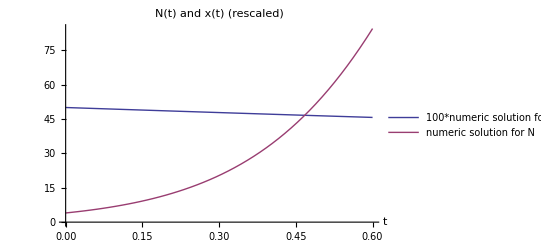

```mathematica
Plot[{100*Evaluate[x[t]/.delta],Evaluate[n[t]/.acca]},{t,0,0.6},PlotLegends->Placed[{"100*numeric solution for x","numeric solution for N"},{0.6,0.8}],AxesLabel->{"t",""},PlotLabel->"N(t) and x(t) (rescaled)"]
```